```mathematica
{d1,d2,d3,d4}=Table[Table[Import["/home/leonard/Documents/Projects/PhysicalDistance/Codes/kickedRotor/data/k_"<>num<>"m_30/"<>fil]//Flatten,{fil,{"clis.dat","qlis.dat","elis.dat"}}],{num,{"0.3","0.5","0.9","1.5"}}];
```

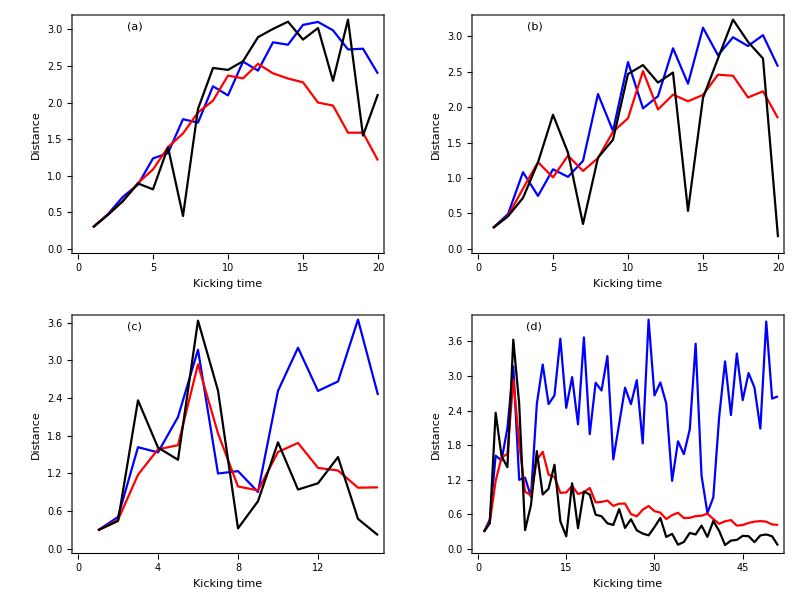
-Graphics- |

```mathematica
fin=Grid[{{Grid[
{
{ListLinePlot[#[[;;20]]&/@d1,{PlotStyle->{Blue,Red,Black},Ticks->{Automatic,{1.0,2.0,3.0}},
FrameStyle->13,
Frame->True,
FrameLabel->{"Kicking time","Distance"},
ImageSize->300,
PlotLegends->Placed["(a)",{0.2,0.95}]}],ListLinePlot[#[[;;20]]&/@d3,{PlotStyle->{Blue,Red,Black},Ticks->{Automatic,{1.0,2.0,3.0}},
FrameStyle->13,
Frame->True,
FrameLabel->{"Kicking time","Distance"},
ImageSize->300,
PlotLegends->Placed["(b)",{0.2,0.95}]}]
},
{ListLinePlot[#[[;;15]]&/@d4,{PlotStyle->{Blue,Red,Black},Ticks->{{4,8,12},{1.,2.,3.}},
FrameStyle->13,
Frame->True,
FrameLabel->{"Kicking time","Distance"},
ImageSize->300,
PlotLegends->Placed["(c)",{0.2,0.95}]}],
ListLinePlot[d4,{PlotStyle->{Blue,Red,Black},
FrameStyle->13,
Frame->True,
FrameLabel->{"Kicking time","Distance"},
ImageSize->300,
PlotLegends->Placed["(d)",{0.2,0.95}]}]}}],
LineLegend[{Blue,Red,Black},{"Classical","Physical","Expectation"},LegendMarkerSize->20]}}]
```

```mathematica
LineLegend[{Blue,Red,Black},{"Classical Distance","Physical Distance","Expectation Distance"}]
```

```mathematica
Export["/home/leonard/Documents/Projects/PhysicalDistance/Paper/figs/krDist.png",fin]
```

/home/leonard/Documents/Projects/PhysicalDistance/Paper/figs/krDist.png